Capacity maximization

```mathematica
h[x_,k_]:=k(theta-alfa*k)*x/(r-mu)-delta k;
Solve[D[h[x,k],k]==0,k]
```

{{k→(delta mu-delta r+theta x)/(2 alfa x)}}

```mathematica
D[h[x,k],{k,2}]
```

-(2 alfa x)/(-mu+r)

Segunda derivada parcial sempre negativa. k definido acima é maximizante.

```mathematica
Kopt=(delta mu-delta r+theta x)/(2 alfa x);
```

```mathematica
Simplify[h[x,Kopt]]
```

-(delta (mu-r)+theta x)^2/(4 alfa (mu-r) x)

```mathematica
Simplify@D[h[x,Kopt],x]
```

(delta^2 (mu-r)^2-theta^2 x^2)/(4 alfa (mu-r) x^2)

```mathematica
xthreshold[d1_,mu_,theta_]:=(d1+1)/(d1-1) delta(r-mu)/theta;
```

```mathematica
sigma=0.005;
mu=0.03;
r=0.05;
delta=2;
alfa=0.01;
theta=10;
```

```mathematica
d1[mu_,sigma_,r_]:=1/2-mu/sigma^2+Sqrt[(1/2-mu/sigma^2)^2+2r/sigma^2];
```

```mathematica
Simplify[xthreshold[d1[mu,sigma,r],mu,theta]]
```

(delta (-mu+r) (3/2+√((-1/2+mu/sigma^2)^2+(2 r)/sigma^2)-mu/sigma^2))/((-1/2+√((-1/2+mu/sigma^2)^2+(2 r)/sigma^2)-mu/sigma^2) theta)

```mathematica
x^*_C
```

```mathematica
Solve[(d1-1)θ^2x^2-(d1-1)2θ δ (r-μ)-(d1-1)δ^2(r-μ)^2==0,x]
```

{{x→-(√(-1+d1) √δ √(r-μ) √(r δ+2 θ-δ μ))/(√(-θ^2+d1 θ^2))},{x→(√(-1+d1) √δ √(r-μ) √(r δ+2 θ-δ μ))/(√(-θ^2+d1 θ^2))}}

```mathematica
Solve[(d1-1)θ^2x^2-2d1 θ δ (r-μ)x+(d1+1)δ^2(r-μ)^2==0,x]
```

{{x→(δ (r-μ))/θ},{x→((1+d1) δ (r-μ))/((-1+d1) θ)}}

```mathematica
Simplify@1/(-θ^2+d1 θ^2)(d1 r δ θ-d1 δ θ μ+√(-r^2 δ^2 θ^2+2 d1^2 r^2 δ^2 θ^2+2 r δ^2 θ^2 μ-4 d1^2 r δ^2 θ^2 μ-δ^2 θ^2 μ^2+2 d1^2 δ^2 θ^2 μ^2))
```

(d1 δ θ (r-μ)+√((-1+2 d1^2) δ^2 θ^2 (r-μ)^2))/((-1+d1) θ^2)

## Comparative Statics

```mathematica
Kopt[x_,mu_,delta_]:=(delta mu-delta r+theta x)/(2 alfa x);
d1[mu_,sigma_,r_]:=1/2-mu/sigma^2+Sqrt[(1/2-mu/sigma^2)^2+2r/sigma^2];
xthreshold[d1_,mu_,theta_]:=(d1+1)/(d1-1) delta(r-mu)/theta;
```

```mathematica
sigma=0.005;
mu=0.03;
r=0.05;
delta=2;
alfa=0.01;
theta=10;
```

### - Parameter d_1

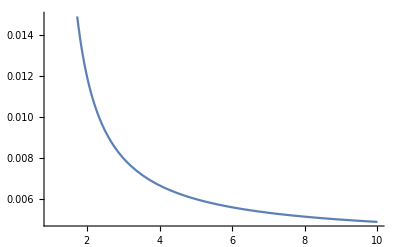

```mathematica
Plot[xthreshold[d1,mu,theta],{d1,1,10}]
```

```mathematica
Manipulate[Plot[d1[mu,sigma,r],{sigma, 0.001,0.5}],{mu,0.0001,r},FrameLabel->"σ"]
```

```mathematica
Plot3D[d1[mu,sigma,r],{sigma, 0.0001,0.5},{mu,0,r},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
mu=0.01;
Manipulate[Plot[d1[mu,sigma,r],{r,mu,0.05}],{sigma, 0.0001,0.5},FrameLabel->"r"]
```

Plot::plln: Limiting value mu in {r, mu, 0.05} is not a machine-sized real number.

```mathematica
sigma=0.05;
Manipulate[Plot[d1[mu,sigma,r],{r,mu,0.05}],{mu, 0,0.5},FrameLabel->"r"]
```

### - Threshold value x*

#### - μ

Threshold value sem capacidade optimizada.

```mathematica
xx[d1_,mu_,theta_,K_]:=(d1+1)/(d1-1) delta(r-mu)/(theta-alfa K);
d1[mu_,sigma_,r_]:=1/2-mu/sigma^2+Sqrt[(1/2-mu/sigma^2)^2+2r/sigma^2];
Simplify[D[xx[d1[mu,sigma,r],mu,theta,k],mu]]
```

(delta √(1+(4 mu^2)/sigma^4-(4 mu)/sigma^2+(8 r)/sigma^2) sigma^2 (-2 mu+sigma^2))/((4 mu^2-4 mu sigma^2+8 r sigma^2+sigma^4) (alfa k-theta))

Threshold value com capacidade optimizada.

```mathematica
Clear[xthreshold];
d1[mu_,sigma_,r_]:=1/2-mu/sigma^2+Sqrt[(1/2-mu/sigma^2)^2+2r/sigma^2];
xthreshold[d1_,mu_,theta_]:=(d1+1)/(d1-1) delta(r-mu)/theta;
```

```mathematica
Simplify[D[xthreshold[d1[mu,sigma,r],mu,theta],mu]]
```

-(delta √(1+(4 mu^2)/sigma^4-(4 mu)/sigma^2+(8 r)/sigma^2) sigma^2 (-2 mu+sigma^2))/((4 mu^2-4 mu sigma^2+8 r sigma^2+sigma^4) theta)

```mathematica
sigma=0.005;
mu=0.03;
r=0.05;
delta=2;
alfa=0.01;
theta=10;
K=100;
```

```mathematica
xx[d1[mu,sigma,r],mu,theta,K]
```

0.017787

```mathematica
Manipulate[Show[Plot[{xthreshold[d1[mu,sigma,r],mu,theta],xx[d1[mu,sigma,r],mu,theta,K]},{mu,-r,r}],
Epilog->{Black, PointSize[0.02],Point[{{sigma^2/2,xx[d1[sigma^2/2,sigma,r],sigma^2/2,theta,K]},{sigma^2/2,xthreshold[d1[sigma^2/2,sigma,r],sigma^2/2,theta]}}]},
Epilog->{Orange, PointSize[0.02],Point[{sigma^2/2,xthreshold[d1[sigma^2/2,sigma,r],sigma^2/2,theta]}]} ],{sigma,  0.0001,1},FrameLabel->"μ"]
```

Plot::plln: Limiting value -r in {mu, -r, r} is not a machine-sized real number.

Show::gtype: Plot is not a type of graphics.

Plot::plln: Limiting value -r in {mu, -r, r} is not a machine-sized real number.

Show::gtype: Plot is not a type of graphics.

Plot::plln: Limiting value -r in {mu, -r, r} is not a machine-sized real number.

Show::gtype: Plot is not a type of graphics.

Plot::plln: Limiting value -r in {mu, -r, r} is not a machine-sized real number.

Show::gtype: Plot is not a type of graphics.

```mathematica
Manipulate[Show[Plot[{xthreshold[d1[mu,sigma,r],mu,theta],xx[d1[mu,sigma,r],mu,theta,K]},{mu,-r,r}],
Epilog->{Black, PointSize[0.02],Point[{{sigma^2/2,xx[d1[sigma^2/2,sigma,r],sigma^2/2,theta,K]},{sigma^2/2,xthreshold[d1[sigma^2/2,sigma,r],sigma^2/2,theta]}}]},
Epilog->{Orange, PointSize[0.02],Point[{sigma^2/2,xthreshold[d1[sigma^2/2,sigma,r],sigma^2/2,theta]}]} ],{K,  0,theta/alfa-1},FrameLabel->"μ"]
```

Plot::plln: Limiting value -r in {mu, -r, r} is not a machine-sized real number.

Show::gtype: Plot is not a type of graphics.

Plot::plln: Limiting value -r in {mu, -r, r} is not a machine-sized real number.

Show::gtype: Plot is not a type of graphics.

Casos particulares relevantes :

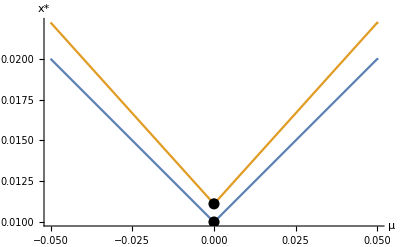

```mathematica
sigma=0.0001;
Show[Plot[{xthreshold[d1[mu,sigma,r],mu,theta],xx[d1[mu,sigma,r],mu,theta,K]},{mu,-r,r}],
Epilog->{Black, PointSize[0.02],Point[{{sigma^2/2,xx[d1[sigma^2/2,sigma,r],sigma^2/2,theta,K]},{sigma^2/2,xthreshold[d1[sigma^2/2,sigma,r],sigma^2/2,theta]}}]},
Epilog->{Orange, PointSize[0.02],Point[{sigma^2/2,xthreshold[d1[sigma^2/2,sigma,r],sigma^2/2,theta]}]} ,AxesLabel->{"μ","x*"}]
```

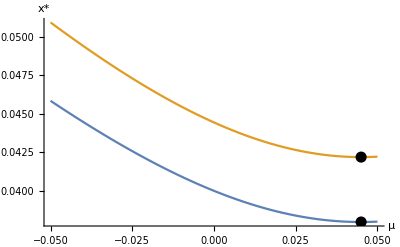

```mathematica
sigma=0.3;
Show[Plot[{xthreshold[d1[mu,sigma,r],mu,theta],xx[d1[mu,sigma,r],mu,theta,K]},{mu,-r,r}(* ,PlotLegends->{"Wo/ capacity max","W/ capacity max"} *) ],
Epilog->{Black, PointSize[0.02],Point[{{sigma^2/2,xx[d1[sigma^2/2,sigma,r],sigma^2/2,theta,K]},{sigma^2/2,xthreshold[d1[sigma^2/2,sigma,r],sigma^2/2,theta]}}]},
Epilog->{Orange, PointSize[0.02],Point[{sigma^2/2,xthreshold[d1[sigma^2/2,sigma,r],sigma^2/2,theta]}]}  ,AxesLabel->{"μ","x*"}]
```

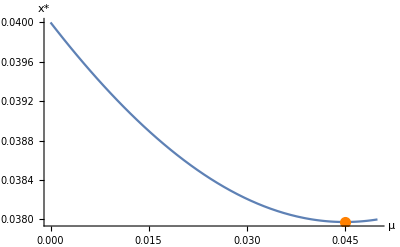

```mathematica
sigma=0.3;
Show[Plot[xthreshold[d1[mu,sigma,r],mu,theta],{mu,0,r}],
Epilog->{Orange, PointSize[0.02],Point[{sigma^2/2,xthreshold[d1[sigma^2/2,sigma,r],sigma^2/2,theta]}]} ,AxesLabel->{"μ","x*"}]
```

#### - σ

Threshold value sem capacidade optimizada.

```mathematica
xx[d1_,mu_,theta_,K_]:=(d1+1)/(d1-1) delta(r-mu)/(theta-alfa K);
d1[mu_,sigma_,r_]:=1/2-mu/sigma^2+Sqrt[(1/2-mu/sigma^2)^2+2r/sigma^2];
Simplify[D[xx[d1[μ,σ,r],μ,theta,k],σ]]
```

-(800. (0.05 μ^2-1. μ^3+0.0025 σ^2-0.075 μ σ^2+0.5 μ^2 σ^2-0.05 μ √((-1/2+μ/σ^2)^2+0.1/σ^2) σ^2+1. μ^2 √((-1/2+μ/σ^2)^2+0.1/σ^2) σ^2))/((-1000.+1. k) √((-1/2+μ/σ^2)^2+0.1/σ^2) σ (1. μ+0.5 σ^2-1. √((-1/2+μ/σ^2)^2+0.1/σ^2) σ^2)^2)

Threshold value com capacidade optimizada.

```mathematica
d1[mu_,sigma_,r_]:=1/2-mu/sigma^2+Sqrt[(1/2-mu/sigma^2)^2+2r/sigma^2];
(*d1alt[mu_,sigma2_,r_]:=1/2-mu/sigma2+Sqrt[(1/2-mu/sigma2)^2+2r/sigma2];*)
xthreshold[d1_,mu_,theta_]:=(d1+1)/(d1-1) delta(r-mu)/theta;
Simplify[D[xthreshold[d1[μ,σ,r],μ,theta],σ]]
(*Simplify[D[xthreshold[d1alt[mu,sigma2,r],mu,theta],sigma2]]*)
```

(0.8 (0.05 μ^2-1. μ^3+0.0025 σ^2-0.075 μ σ^2+0.5 μ^2 σ^2-0.05 μ √((-1/2+μ/σ^2)^2+0.1/σ^2) σ^2+1. μ^2 √((-1/2+μ/σ^2)^2+0.1/σ^2) σ^2))/(√((-1/2+μ/σ^2)^2+0.1/σ^2) σ (1. μ+0.5 σ^2-1. √((-1/2+μ/σ^2)^2+0.1/σ^2) σ^2)^2)

```mathematica
Clear[sigma]
```

```mathematica
Solve[-2 mu^2-2 r sigma^2+mu (1+√(1+(4 mu^2)/sigma^4-(4 mu)/sigma^2+(8 r)/sigma^2)) sigma^2==0,sigma]
```

{}

```mathematica
sigma=0.005;
mu=0.03;
r=0.05;
delta=2;
alfa=0.01;
theta=10;
K=100
```

100

```mathematica
Manipulate[Show[Plot[{xthreshold[d1[mu,sigma,r],mu,theta],xx[d1[mu,sigma,r],mu,theta,K]},{sigma,  0.0001,1}]],{mu,-1,r},FrameLabel->"σ"]
```

```mathematica
(0.5-d1[m,s,R])*s
```

(0.-√((1/2-m/s^2)^2+(2 R)/s^2)+m/s^2) s

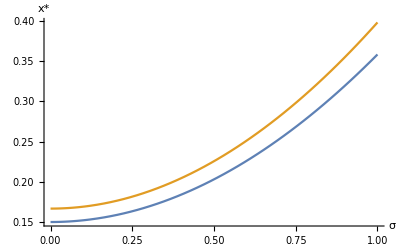

```mathematica
mu=-0.7;
Show[Plot[{xthreshold[d1[mu,sigma,r],mu,theta],xx[d1[mu,sigma,r],mu,theta,K]},{sigma,0.0001,1}],AxesLabel->{"σ","x*"}]
```

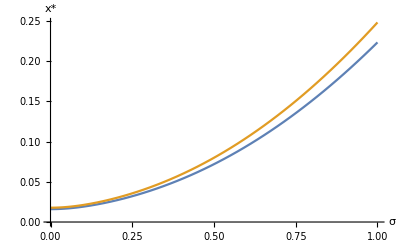

```mathematica
mu=0.03;
Show[Plot[{xthreshold[d1[mu,sigma,r],mu,theta],xx[d1[mu,sigma,r],mu,theta,K]},{sigma,0.0001,1}],AxesLabel->{"σ","x*"}]
```

#### - δ

```mathematica
d1[mu_,sigma_,r_]:=1/2-mu/sigma^2+Sqrt[(1/2-mu/sigma^2)^2+2r/sigma^2];
(*d1alt[mu_,sigma2_,r_]:=1/2-mu/sigma2+Sqrt[(1/2-mu/sigma2)^2+2r/sigma2];*)
xthreshold[d1_,mu_,theta_]:=(d1+1)/(d1-1) delta(r-mu)/theta;
Simplify[D[xthreshold[d1[μ,σ,r],μ,theta],delta]]
(*Simplify[D[xthreshold[d1alt[mu,sigma2,r],mu,theta],sigma2]]*)
```

((r-μ) (3/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2))/(theta (-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2))

```mathematica
Manipulate[Show[Plot[xthreshold[d1[mu,sigma,r],mu,theta],{delta,0,1}]],{sigma,  0.0001,1},FrameLabel->"δ"]
```

```mathematica
Manipulate[Show[Plot[xthreshold[d1[mu,sigma,r],mu,theta],{delta,0,1}]],{mu,  0,r},FrameLabel->"μ"]
```

#### - K

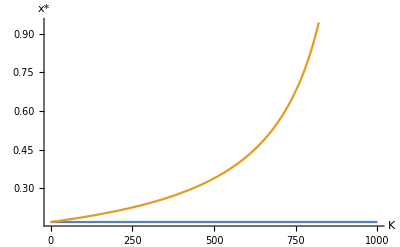

```mathematica
Plot[{xthreshold[d1[mu,sigma,r],mu,theta],xx[d1[mu,sigma,r],mu,theta,K]},{K,0,theta/alfa},AxesLabel->{"K","x*"}]
```

#### - δ

```mathematica
xthresholdD[d1_,mu_,theta_,delta_]:=(d1+1)/(d1-1) delta(r-mu)/theta;
xxD[d1_,mu_,theta_,K_,delta_]:=(d1+1)/(d1-1) delta(r-mu)/(theta-alfa K);
```

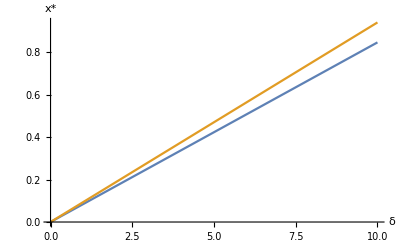

```mathematica
Plot[{xthresholdD[d1[mu,sigma,r],mu,theta,delta],xxD[d1[mu,sigma,r],mu,theta,K,delta]},{delta,0, 10},AxesLabel->{"δ","x*"}]
```

#### - θ

```mathematica
alfa*K
```

1.

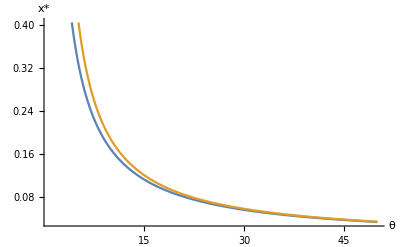

```mathematica
Plot[{xthreshold[d1[mu,sigma,r],mu,theta],xx[d1[mu,sigma,r],mu,theta,K]},{theta,alfa*K,50 },AxesLabel->{"θ","x*"}]
```

```mathematica
xthreshold[d1[mu,sigma,r],mu,alfa*K]
```

1.69203

### - Optimal capacity K* and K*(x*)

```mathematica
Simplify[Kopt[xthreshold[d1[μ,σ,r],μ,theta],μ,delta]]
```

(2 theta σ^2)/(alfa (-2 μ+(3+√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)) σ^2))

#### - μ

```mathematica
Clear[xthreshold];
Kopt[x_,mu_,delta_]:=(delta mu-delta r+theta x)/(2 alfa x);
d1[mu_,sigma_,r_]:=1/2-mu/sigma^2+Sqrt[(1/2-mu/sigma^2)^2+2r/sigma^2];
xthreshold[d1_,mu_,theta_]:=(d1+1)/(d1-1) delta(r-mu)/theta;
```

```mathematica
Simplify[D[Kopt[x],mu]]
Simplify[D[Kopt[x],x]]
```

delta/(2 alfa x)

(delta (-mu+r))/(2 alfa x^2)

(4 (-2 mu+(1+√(1+(4 mu^2)/sigma^4-(4 mu)/sigma^2+(8 r)/sigma^2)) sigma^2) theta)/(alfa √(1+(4 mu^2)/sigma^4-(4 mu)/sigma^2+(8 r)/sigma^2) (-2 mu+(3+√(1+(4 mu^2)/sigma^4-(4 mu)/sigma^2+(8 r)/sigma^2)) sigma^2)^2)

```mathematica
Simplify@@{D[Kopt[xthreshold[d1[μ,σ,r],μ,theta],μ,delta],μ]}
```

(4 theta (-2 μ+(1+√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)) σ^2))/(alfa √(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) (-2 μ+(3+√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)) σ^2)^2)

```mathematica
Manipulate[Show[Plot[Kopt[xthreshold[d1[mu,sigma,r],mu,theta],mu,delta],{mu,0,r}]],{sigma,  0.0001,1},FrameLabel->"μ"]
```

Plot::plln: Limiting value r in {mu, 0, r} is not a machine-sized real number.

Show::gtype: Plot is not a type of graphics.

Plot::plln: Limiting value r in {mu, 0, r} is not a machine-sized real number.

Show::gtype: Plot is not a type of graphics.

Plot::plln: Limiting value r in {mu, 0, r} is not a machine-sized real number.

Show::gtype: Plot is not a type of graphics.

Plot::plln: Limiting value r in {mu, 0, r} is not a machine-sized real number.

Show::gtype: Plot is not a type of graphics.

Plot::plln: Limiting value r in {mu, 0, r} is not a machine-sized real number.

Show::gtype: Plot is not a type of graphics.

Plot::plln: Limiting value r in {mu, 0, r} is not a machine-sized real number.

Show::gtype: Plot is not a type of graphics.

Plot::plln: Limiting value r in {mu, 0, r} is not a machine-sized real number.

Show::gtype: Plot is not a type of graphics.

Plot::plln: Limiting value r in {mu, 0, r} is not a machine-sized real number.

Show::gtype: Plot is not a type of graphics.

Plot::plln: Limiting value r in {mu, 0, r} is not a machine-sized real number.

Show::gtype: Plot is not a type of graphics.

Plot::plln: Limiting value r in {mu, 0, r} is not a machine-sized real number.

Show::gtype: Plot is not a type of graphics.

Plot::plln: Limiting value r in {mu, 0, r} is not a machine-sized real number.

Show::gtype: Plot is not a type of graphics.

Plot::plln: Limiting value r in {mu, 0, r} is not a machine-sized real number.

Show::gtype: Plot is not a type of graphics.

Plot::plln: Limiting value r in {mu, 0, r} is not a machine-sized real number.

Show::gtype: Plot is not a type of graphics.

Plot::plln: Limiting value r in {mu, 0, r} is not a machine-sized real number.

Show::gtype: Plot is not a type of graphics.

Plot::plln: Limiting value r in {mu, 0, r} is not a machine-sized real number.

Show::gtype: Plot is not a type of graphics.

Plot::plln: Limiting value r in {mu, 0, r} is not a machine-sized real number.

Show::gtype: Plot is not a type of graphics.

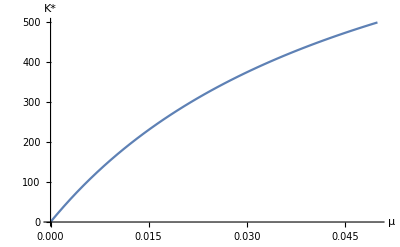

```mathematica
sigma=0.0001;
Plot[Kopt[xthreshold[d1[mu,sigma,r],mu,theta],mu,delta],{mu,0,r},AxesLabel->{"μ","K*"}]
```

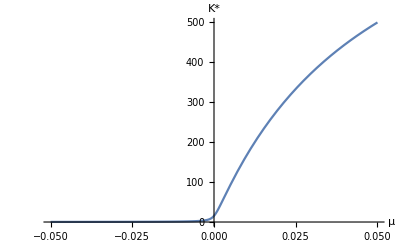

```mathematica
sigma=0.005;
Plot[Kopt[xthreshold[d1[mu,sigma,r],mu,theta],mu,delta],{mu,-r,r},AxesLabel->{"μ","K*"}]
```

#### - σ

```mathematica
Simplify[D[Kopt[x],sigma]]
Simplify@@{D[Kopt[x,μ,delta],σ]}
Simplify@@{D[Kopt[xthreshold[d1[μ,σ,r],μ,theta],μ,delta],σ]}
```

0

0

-(8 theta (-2 μ^2-2 r σ^2+μ (1+√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)) σ^2))/(alfa √(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ (-2 μ+(3+√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)) σ^2)^2)

```mathematica
Manipulate[Show[Plot[Kopt[xthreshold[d1[mu,sigma,r],mu,theta],mu,delta],{sigma,  0.0001,1}]],{mu,0,r},FrameLabel->"σ"]
```

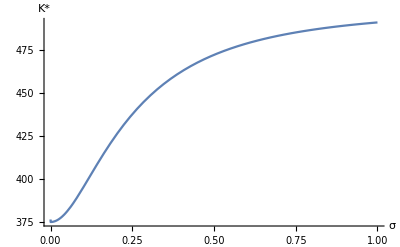

```mathematica
mu=0.03;
Plot[Kopt[xthreshold[d1[mu,sigma,r],mu,theta],mu,delta],{sigma,0,1},AxesLabel->{"σ","K*"}]
```

#### - r

```mathematica
KoptD[x_,mu_,delta_,r_,alfa_]:=(delta mu-delta r+theta x)/(2 alfa x);
```

0.003

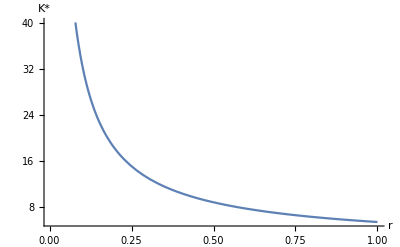

```mathematica
mu=0.003
Plot[KoptD[xthreshold[d1[mu,sigma,r],mu,theta],mu,delta,r,alfa],{r,mu,1},AxesLabel->{"r","K*"}]
```

#### - α

```mathematica
KoptD[x_,mu_,delta_,r_,alfa_]:=(delta mu-delta r+theta x)/(2 alfa x);
```

0.003

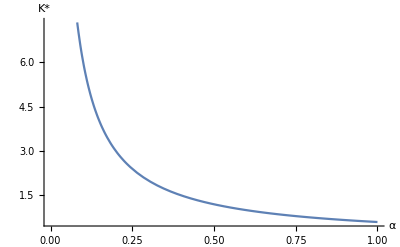

```mathematica
mu=0.003
Plot[KoptD[xthreshold[d1[mu,sigma,r],mu,theta],mu,delta,r,alfa],{alfa,0,1},AxesLabel->{"α","K*"}]
```